### 90° Hybrid (NOT DONE)

From Bahl, chapter 12

First we analyse an arm of the hybrid. It is either a waveguide, or a lumped π network. Let us see the relation:

```mathematica
w=CircuitExpression[TwoportWaveguide[z0,θ/l,l],ω]
```

^A{{Cos[θ],ⅈ z0 Sin[θ]},{(ⅈ Sin[θ])/z0,Cos[θ]}}

```mathematica
p=CircuitExpression[TwoportPi[OneportC[c1],OneportL[l1],OneportC[c1]],ω]//FullSimplify
```

^A{{1-c1 l1 ω^2,ⅈ l1 ω},{-ⅈ c1 ω (-2+c1 l1 ω^2),1-c1 l1 ω^2}}

```mathematica
MapThread[Equal,{Flatten[List@@w],Flatten[List@@p]}]
```

{Cos[θ]==1-c1 l1 ω^2,ⅈ z0 Sin[θ]==ⅈ l1 ω,(ⅈ Sin[θ])/z0==-ⅈ c1 ω (-2+c1 l1 ω^2),Cos[θ]==1-c1 l1 ω^2}

```mathematica
Solve[MapThread[Equal,{Flatten[List@@w],Flatten[List@@p]}],{θ,z0,l1}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{z0→(√(1-Cos[θ]^2))/(c1 ω+c1 ω Cos[θ]),l1→(1-Cos[θ]^2)/(ω (c1 ω+c1 ω Cos[θ]))},{z0→(√(1-Cos[θ]^2))/(-c1 ω-c1 ω Cos[θ]),l1→(1-Cos[θ]^2)/(c1 ω^2+c1 ω^2 Cos[θ])}}

### Directional coupler (NOT DONE)

### Waveguide vs Network (NOT DONE)

```mathematica
param={z0->50.,θ->20.};
CircuitExpression[TwoportWaveguide[z0,θ/l,l],ω]
CircuitExpression[TwoportPi[OneportC[1/z0 √((1-Cos[θ])/(1+Cos[θ]))],OneportL[(z0 Sin[θ])/ω],OneportC[1/z0 √((1-Cos[θ])/(1+Cos[θ]))]],ω]
```

^A{{Cos[θ],ⅈ z0 Sin[θ]},{(ⅈ Sin[θ])/z0,Cos[θ]}}

^A{{1-ω √((1-Cos[θ])/(1+Cos[θ])) Sin[θ],ⅈ z0 Sin[θ]},{(ⅈ ω √((1-Cos[θ])/(1+Cos[θ])))/z0+(ⅈ ω √((1-Cos[θ])/(1+Cos[θ])) (1-ω √((1-Cos[θ])/(1+Cos[θ])) Sin[θ]))/z0,1-ω √((1-Cos[θ])/(1+Cos[θ])) Sin[θ]}}

### A cable trap (NOT DONE)

```mathematica
cableCircuit=TwoportXsection[OneportC[c1],OneportL[l1]]
```

TwoportXsection[OneportC[c1],OneportL[l1]]

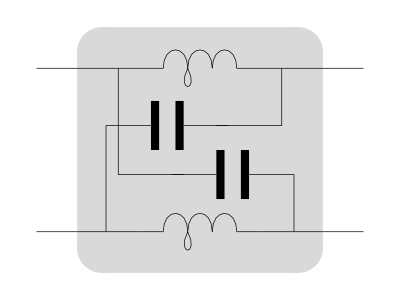

```mathematica
CircuitGraphics[cableCircuit]
```

```mathematica
cableCircuitExpression=CircuitExpression[cableCircuit,ω]/.{l1->10^(-9),c1->10^(-12)}
```

^A{{(-(1000000000000 ⅈ)/ω+(ⅈ ω)/1000000000)/(-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000),2000/(-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000)},{2/(-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000),(-(1000000000000 ⅈ)/ω+(ⅈ ω)/1000000000)/(-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000)}}

```mathematica
cableCircuitExpressionSparam=ToS[cableCircuitExpression,{50.,50}]//Chop
```

^S{{-(60/((140/(-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000)+(2 (-(1000000000000 ⅈ)/ω+(ⅈ ω)/1000000000))/(-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000)) (-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000))),(2. (-4000/(-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000)^2+(-(1000000000000 ⅈ)/ω+(ⅈ ω)/1000000000)^2/(-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000)^2))/(140/(-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000)+(2 (-(1000000000000 ⅈ)/ω+(ⅈ ω)/1000000000))/(-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000))},{2./(140/(-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000)+(2 (-(1000000000000 ⅈ)/ω+(ⅈ ω)/1000000000))/(-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000)),-(60/((140/(-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000)+(2 (-(1000000000000 ⅈ)/ω+(ⅈ ω)/1000000000))/(-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000)) (-(1000000000000 ⅈ)/ω-(ⅈ ω)/1000000000)))}}

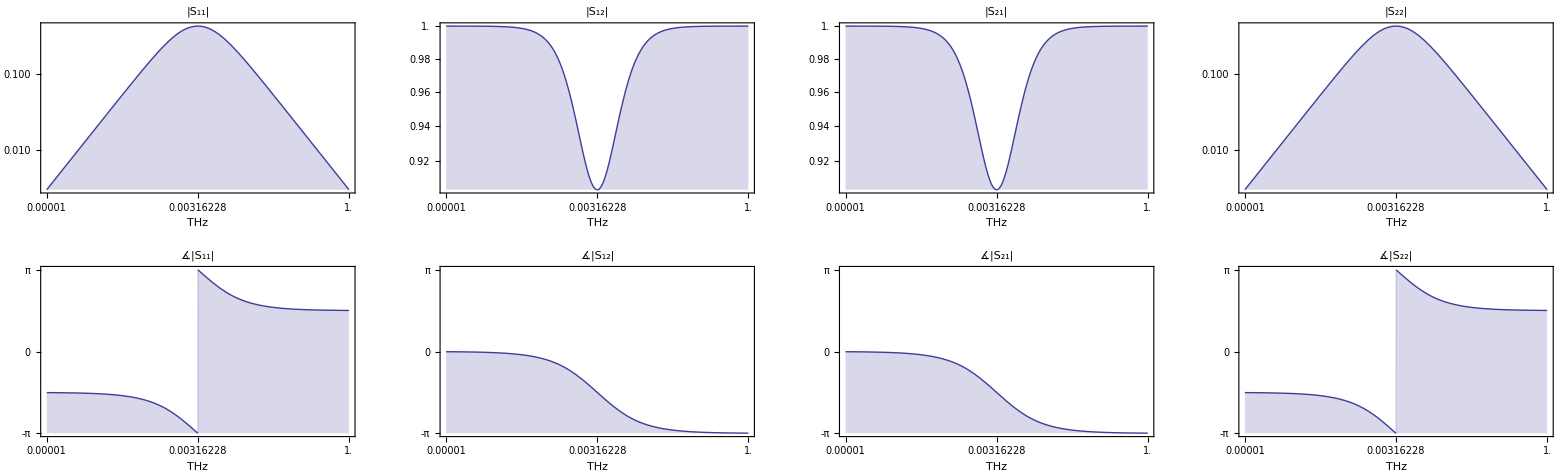

```mathematica
omin=10^8;omax=1 10^13;


LogLinearPlotSparameters[cableCircuitExpressionSparam,{ω,omin,omax}]
```

### A bridge circuit

```mathematica
bridgeCircuit=CircuitCascade[TwoportBridge[OneportR[r1],OneportR[r2],OneportR[r3],OneportR[r4]],TwoportShunt[OneportParallel[OneportL[l1],OneportC[c1]]]]
```

CircuitCascade[TwoportBridge[OneportR[r1],OneportR[r2],OneportR[r3],OneportR[r4]],TwoportShunt[OneportParallel[OneportL[l1],OneportC[c1]]]]

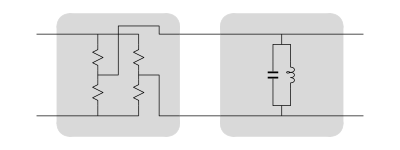

```mathematica
CircuitGraphics[bridgeCircuit]
```

```mathematica
bridgeCircuitExpression=CircuitExpression[bridgeCircuit,ω]/.{r1->10000,r2->20000,r3->10000,r4->40000,l1->10^(-9),c1->10^(-12)}
```

^A{{-15/2-110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000),-110000},{-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000),-6}}

```mathematica
bridgeCircuitExpressionSparam=ToS[bridgeCircuitExpression,{50.,1. 10^18}]//Chop
```

^S{{(-4403/2-50 (-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))-110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))/(-4427/2+50 (-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))-110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000)),(1.41421×10^-8 (-6 (-15/2-110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))+110000 (-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))))/(-4427/2+50 (-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))-110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))},{2.82843×10^8/(-4427/2+50 (-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))-110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000)),(-4397/2-50 (-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))+110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))/(-4427/2+50 (-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))-110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))}}

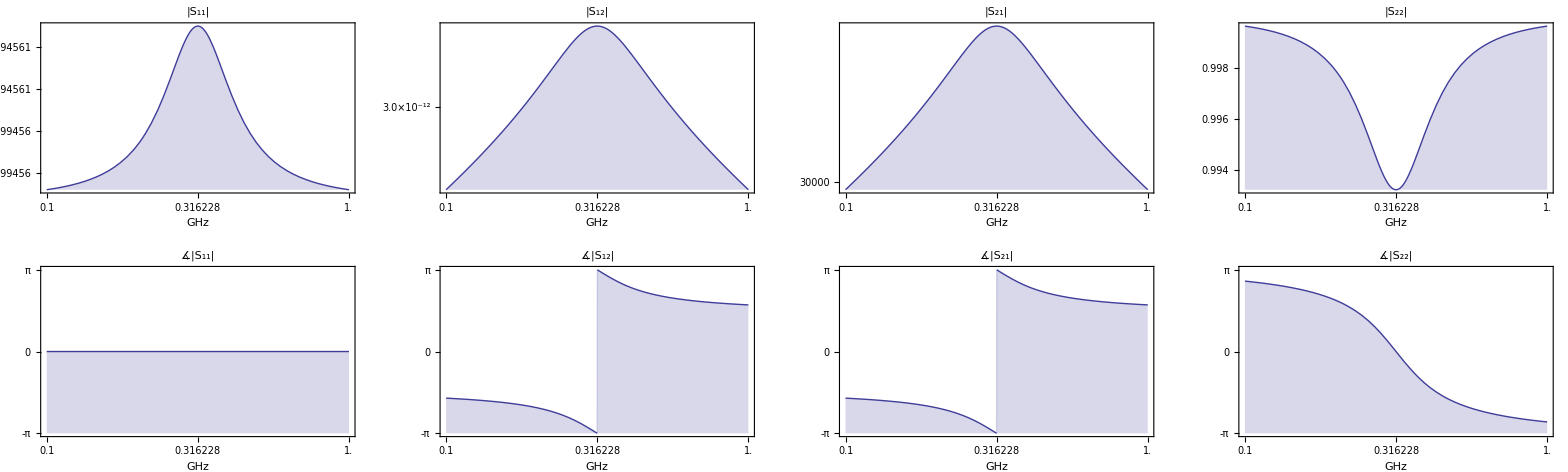

```mathematica
omin=10^10;omax=1 10^11;
LogLinearPlotSparameters[bridgeCircuitExpressionSparam,{ω,omin,omax}]
```

### MR sensor

CircuitCascade[TwoportShunt[OneportC[c1]],CircuitCascade[TwoportSeries[OneportC[c1]],TwoportShunt[OneportL[l1]]]]

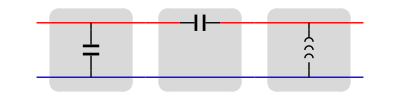

Export::nodir: Directory /Users/Jan G. Korvink/Desktop/DT/3 Temp Docs/CircuitTheory/ does not exist.

Export::noopen: Cannot open /Users/Jan G. Korvink/Desktop/DT/3 Temp Docs/CircuitTheory/mrcircuitpic.pdf.

$Failed

^A{{1-1/(c1 l1 ω^2),-ⅈ/(c1 ω)},{-ⅈ/(l1 ω)+ⅈ c1 (1-1/(c1 l1 ω^2)) ω,2}}

(1-1/(c1 l1 ω^2) | -ⅈ/(c1 ω)
-ⅈ/(l1 ω)+ⅈ c1 (1-1/(c1 l1 ω^2)) ω | 2)

^S{{(-1-1/(c1 l1 ω^2)-ⅈ/(50 c1 ω)-50 (-ⅈ/(l1 ω)+ⅈ c1 (1-1/(c1 l1 ω^2)) ω))/(3-1/(c1 l1 ω^2)-ⅈ/(50 c1 ω)+50 (-ⅈ/(l1 ω)+ⅈ c1 (1-1/(c1 l1 ω^2)) ω)),(0.00447214 (2 (1-1/(c1 l1 ω^2))+(ⅈ (-ⅈ/(l1 ω)+ⅈ c1 (1-1/(c1 l1 ω^2)) ω))/(c1 ω)))/(3-1/(c1 l1 ω^2)-ⅈ/(50 c1 ω)+50 (-ⅈ/(l1 ω)+ⅈ c1 (1-1/(c1 l1 ω^2)) ω))},{894.427/(3-1/(c1 l1 ω^2)-ⅈ/(50 c1 ω)+50 (-ⅈ/(l1 ω)+ⅈ c1 (1-1/(c1 l1 ω^2)) ω)),(1+1/(c1 l1 ω^2)-ⅈ/(50 c1 ω)-50 (-ⅈ/(l1 ω)+ⅈ c1 (1-1/(c1 l1 ω^2)) ω))/(3-1/(c1 l1 ω^2)-ⅈ/(50 c1 ω)+50 (-ⅈ/(l1 ω)+ⅈ c1 (1-1/(c1 l1 ω^2)) ω))}}

```mathematica
MRCircuit=CircuitCascade[TwoportShunt[OneportC[c1]] ,CircuitCascade[TwoportSeries[OneportC[c1]] ,TwoportShunt[OneportL[l1]]]]
mrcircuitpic=CircuitGraphics[MRCircuit]
Export["/Users/Jan G. Korvink/Desktop/DT/3 Temp Docs/CircuitTheory/mrcircuitpic.pdf",mrcircuitpic]
MRCircuitExpression=CircuitExpression[MRCircuit,ω]
MatrixForm[MRCircuitExpression]
MRCircuitExpressionSparam=ToS[MRCircuitExpression,{50.,1. 10^7}]//Chop
MRCircuitParameters={c1->10. 10^-10,l1->.2 10^-6};
```

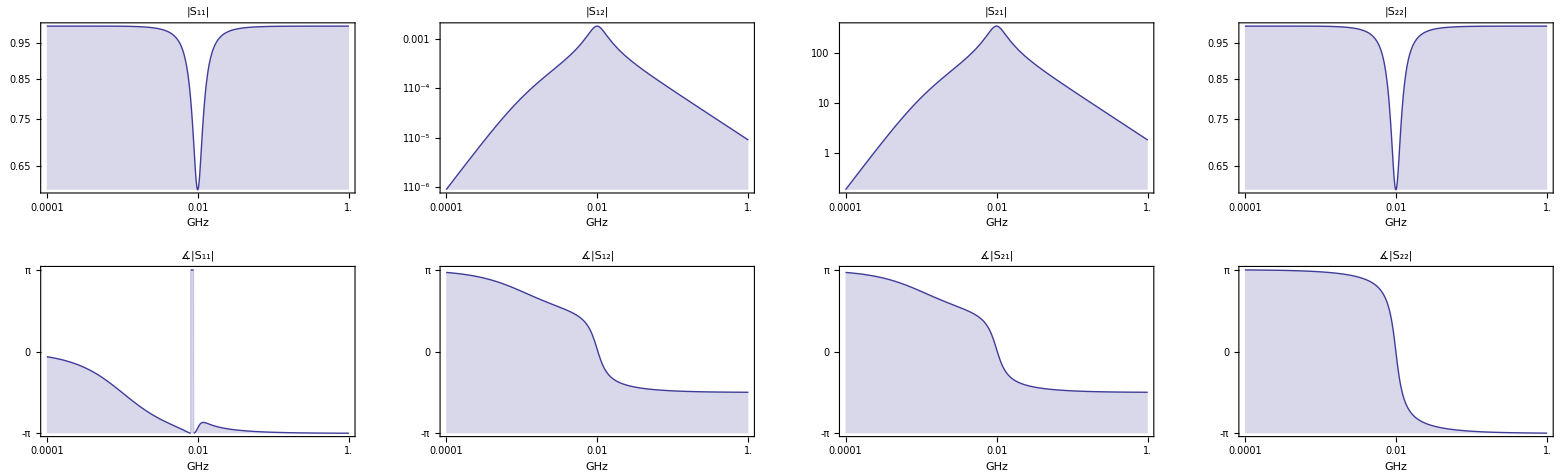

```mathematica
LogLinearPlotSparameters[MRCircuitExpressionSparam/.MRCircuitParameters,{ω,1 10^6, 10^10}]
```

### MR sensor with balanced output

CircuitCascade[TwoportBoxsection[OneportC[c1],OneportC[c2]],CircuitCascade[TwoportSeries[OneportC[c3]],TwoportShunt[OneportL[l1]]]]

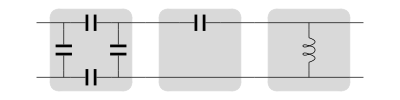

Export::nodir: Directory "/Users/Jan G. Korvink/Desktop/DT/3 Temp Docs/CircuitTheory/" does not exist.

Export::noopen: Cannot open "/Users/Jan G. Korvink/Desktop/DT/3 Temp Docs/CircuitTheory/mrcircuitpic.pdf".

$Failed

2 ^A{{((c1+c2) (1-1/(c3 l1 ω^2)))/c1-1/(c1 l1 ω^2),-ⅈ/(c1 ω)-(ⅈ (c1+c2))/(c1 c3 ω)},{-(ⅈ (c1+c2))/(c1 l1 ω)+(ⅈ c2 (2 c1+c2) (1-1/(c3 l1 ω^2)) ω)/c1,(c1+c2)/c1+(c2 (2 c1+c2))/(c1 c3)}}

2 ^A{{((c1+c2) (1-1/(c3 l1 ω^2)))/c1-1/(c1 l1 ω^2),-ⅈ/(c1 ω)-(ⅈ (c1+c2))/(c1 c3 ω)},{-(ⅈ (c1+c2))/(c1 l1 ω)+(ⅈ c2 (2 c1+c2) (1-1/(c3 l1 ω^2)) ω)/c1,(c1+c2)/c1+(c2 (2 c1+c2))/(c1 c3)}}

ToS[2 ^A{{((c1+c2) (1-1/(c3 l1 ω^2)))/c1-1/(c1 l1 ω^2),-ⅈ/(c1 ω)-(ⅈ (c1+c2))/(c1 c3 ω)},{-(ⅈ (c1+c2))/(c1 l1 ω)+(ⅈ c2 (2 c1+c2) (1-1/(c3 l1 ω^2)) ω)/c1,(c1+c2)/c1+(c2 (2 c1+c2))/(c1 c3)}},{50.,1.×10^7}]

```mathematica
MRCircuit=CircuitCascade[TwoportBoxsection[OneportC[c1],OneportC[c2]] ,CircuitCascade[TwoportSeries[OneportC[c3]],TwoportShunt[OneportL[l1]]]]
mrcircuitpic=CircuitGraphics[MRCircuit]
Export["/Users/Jan G. Korvink/Desktop/DT/3 Temp Docs/CircuitTheory/mrcircuitpic.pdf",mrcircuitpic]
MRCircuitExpression=CircuitExpression[MRCircuit,ω]
MatrixForm[MRCircuitExpression]
MRCircuitExpressionSparam=ToS[MRCircuitExpression,{50.,1. 10^7}]//Chop
MRCircuitParameters={c1->10. 10^-15,c2->10. 10^-15,c3->10. 10^-12,l1->.2 10^-6};
```

```mathematica
LogLinearPlotSparameters[MRCircuitExpressionSparam/.MRCircuitParameters,{ω,1 10^8, 10^10}]
```

LogLinearPlotSparameters[ToS[2 ^A{{2. (1-(5.×10^17)/ω^2)-(5.×10^20)/ω^2,-(0.+1.002×10^14 ⅈ)/ω},{-(0.+1.×10^7 ⅈ)/ω+(0.+3.×10^-14 ⅈ) (1-(5.×10^17)/ω^2) ω,2.003}},{50.,1.×10^7}],{ω,100000000,10000000000}]

```mathematica
CircuitExpression[TwoportBoxsection[OneportC[c1],OneportC[c2]],ω]
```

2 ^A{{(c1+c2)/c1,-ⅈ/(c1 ω)},{ⅈ c2 ω+(ⅈ c2 (c1+c2) ω)/c1,1+c2/c1}}

### Impedance spectroscopy (NOT DONE)

### Patrick Bollgrün’s flux guide

```mathematica
BasicCircuitParameters={c1->75. 10^-12,l1->80. 10^-9,m1->8. 10^-9,r1->.1};
```

```mathematica
baseCircuit=
CircuitCascade[TwoportSeries[OneportR[r1]],CircuitCascade[TwoportSeries[OneportC[c1]],CircuitCascade[TwoportSeries[OneportL[l1]] ,TwoportShunt[OneportL[m1]]]]]
```

CircuitCascade[TwoportSeries[OneportR[r1]],CircuitCascade[TwoportSeries[OneportC[c1]],CircuitCascade[TwoportSeries[OneportL[l1]],TwoportShunt[OneportL[m1]]]]]

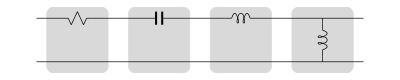

```mathematica
CircuitGraphics[baseCircuit,Frame->False]
```

```mathematica
doubleCircuit=CircuitCascade[baseCircuit,baseCircuit]
```

CircuitCascade[CircuitCascade[TwoportSeries[OneportR[r1]],CircuitCascade[TwoportSeries[OneportC[c1]],CircuitCascade[TwoportSeries[OneportL[l1]],TwoportShunt[OneportL[m1]]]]],CircuitCascade[TwoportSeries[OneportR[r1]],CircuitCascade[TwoportSeries[OneportC[c1]],CircuitCascade[TwoportSeries[OneportL[l1]],TwoportShunt[OneportL[m1]]]]]]

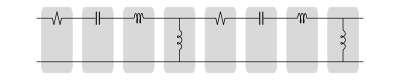

```mathematica
CircuitGraphics[doubleCircuit,Frame->False]
```

CircuitCascade[CircuitCascade[CircuitCascade[TwoportSeries[OneportR[r1]],CircuitCascade[TwoportSeries[OneportC[c1]],CircuitCascade[TwoportSeries[OneportL[l1]],TwoportShunt[OneportL[m1]]]]],CircuitCascade[TwoportSeries[OneportR[r1]],CircuitCascade[TwoportSeries[OneportC[c1]],CircuitCascade[TwoportSeries[OneportL[l1]],TwoportShunt[OneportL[m1]]]]]],CircuitCascade[CircuitCascade[TwoportSeries[OneportR[r1]],CircuitCascade[TwoportSeries[OneportC[c1]],CircuitCascade[TwoportSeries[OneportL[l1]],TwoportShunt[OneportL[m1]]]]],CircuitCascade[TwoportSeries[OneportR[r1]],CircuitCascade[TwoportSeries[OneportC[c1]],CircuitCascade[TwoportSeries[OneportL[l1]],TwoportShunt[OneportL[m1]]]]]]]

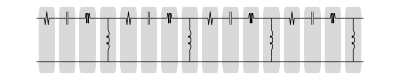

```mathematica
quadCircuit=CircuitCascade[doubleCircuit,doubleCircuit]
CircuitGraphics[quadCircuit,Frame->False]
```

```mathematica
baseCircuitExpression=CircuitExpression[baseCircuit,(2π) f]/.BasicCircuitParameters;
```

```mathematica
doubleCircuitExpression=CircuitExpression[doubleCircuit,(2π) f]/.BasicCircuitParameters;
```

```mathematica
quadCircuitExpression=CircuitExpression[quadCircuit,(2π)f]/.BasicCircuitParameters;
```

```mathematica
baseCircuitExpressionSparam=ToS[baseCircuitExpression,{50.,1. 10^9}];
```

```mathematica
doubleCircuitExpressionSparam=ToS[doubleCircuitExpression,{50.,1. 10^9}];
```

```mathematica
quadCircuitExpression
```

^A{{-1/f^6(0.+7.52432×10^49 ⅈ) (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)^2+1/f^8 3.17655×10^66 (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2)^2,1/f^5 3.78213×10^42 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)+1/f^7 1.59671×10^59 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2)},{-1/f^5(0.+3.54575×10^40 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)-1/f^7(0.+1.49692×10^57 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2),1/f^4 1.78229×10^33 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2-1/f^6(0.+7.52432×10^49 ⅈ) (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)^2}}

```mathematica
quadCircuitExpressionSparam=ToS[quadCircuitExpression,{50.,1. 10^9}]
```

^S{{((0.+0. ⅈ)-1/f^4 1.78229×10^33 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2+1/f^83.17655×10^66 (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2)^2-50 (-1/f^5(0.+3.54575×10^40 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)-1/f^7(0.+1.49692×10^57 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2))+1/50 (1/f^53.78213×10^42 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)+1/f^71.59671×10^59 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2)))/(1/f^4 1.78229×10^33 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2-1/f^6(0.+1.50486×10^50 ⅈ) (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)^2+1/f^83.17655×10^66 (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2)^2+50 (-1/f^5(0.+3.54575×10^40 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)-1/f^7(0.+1.49692×10^57 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2))+1/50 (1/f^53.78213×10^42 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)+1/f^71.59671×10^59 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2))),(0.000447214 (-(-1/f^5(0.+3.54575×10^40 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)-1/f^7(0.+1.49692×10^57 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2)) (1/f^53.78213×10^42 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)+1/f^71.59671×10^59 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2))+(1/f^4 1.78229×10^33 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2-1/f^6(0.+7.52432×10^49 ⅈ) (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)^2) (-1/f^6(0.+7.52432×10^49 ⅈ) (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)^2+1/f^83.17655×10^66 (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2)^2)))/(1/f^4 1.78229×10^33 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2-1/f^6(0.+1.50486×10^50 ⅈ) (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)^2+1/f^83.17655×10^66 (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2)^2+50 (-1/f^5(0.+3.54575×10^40 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)-1/f^7(0.+1.49692×10^57 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2))+1/50 (1/f^53.78213×10^42 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)+1/f^71.59671×10^59 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2)))},{8944.27/(1/f^4 1.78229×10^33 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2-1/f^6(0.+1.50486×10^50 ⅈ) (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)^2+1/f^83.17655×10^66 (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2)^2+50 (-1/f^5(0.+3.54575×10^40 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)-1/f^7(0.+1.49692×10^57 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2))+1/50 (1/f^53.78213×10^42 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)+1/f^71.59671×10^59 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2))),((0.+0. ⅈ)+1/f^4 1.78229×10^33 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2-1/f^83.17655×10^66 (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2)^2-50 (-1/f^5(0.+3.54575×10^40 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)-1/f^7(0.+1.49692×10^57 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2))+1/50 (1/f^53.78213×10^42 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)+1/f^71.59671×10^59 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2)))/(1/f^4 1.78229×10^33 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2-1/f^6(0.+1.50486×10^50 ⅈ) (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)^2+1/f^83.17655×10^66 (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2)^2+50 (-1/f^5(0.+3.54575×10^40 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)-1/f^7(0.+1.49692×10^57 ⅈ) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2))+1/50 (1/f^53.78213×10^42 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f)+1/f^71.59671×10^59 (-ⅈ+4.71239×10^-10 (0.1+(0.+5.02655×10^-7 ⅈ) f) f) (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+6.03186×10^-7 f) f) (2.36871×10^-17 f^2 (-1+4.71239×10^-10 ((0.-0.1 ⅈ)+5.02655×10^-7 f) f)+(1-4.71239×10^-10 ((0.-0.1 ⅈ)+5.5292×10^-7 f) f)^2)))}}

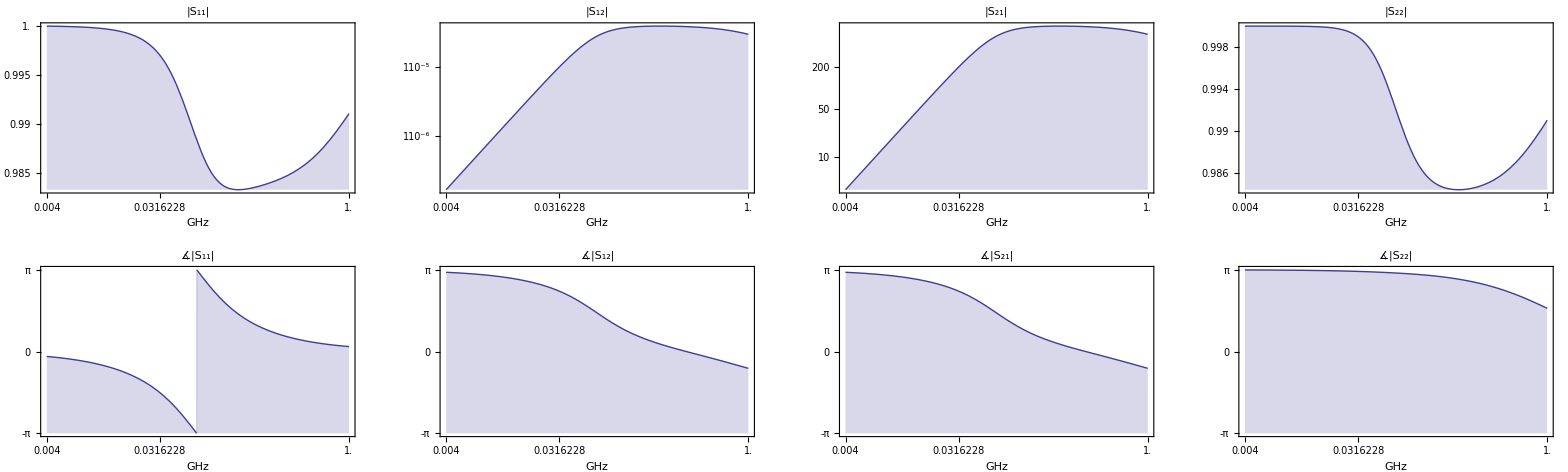

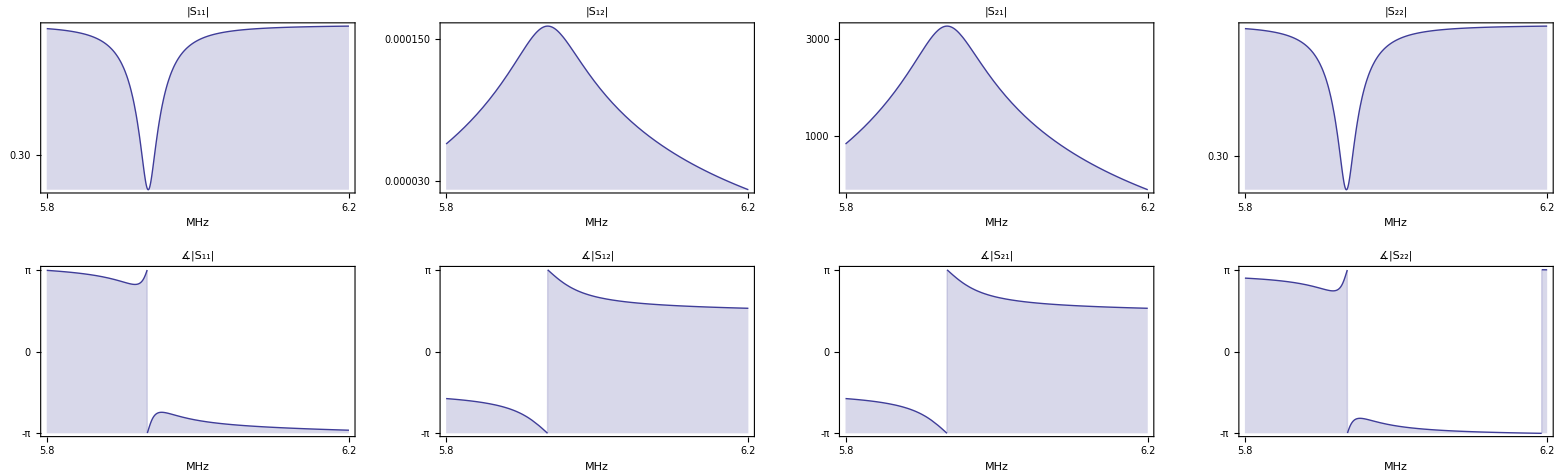

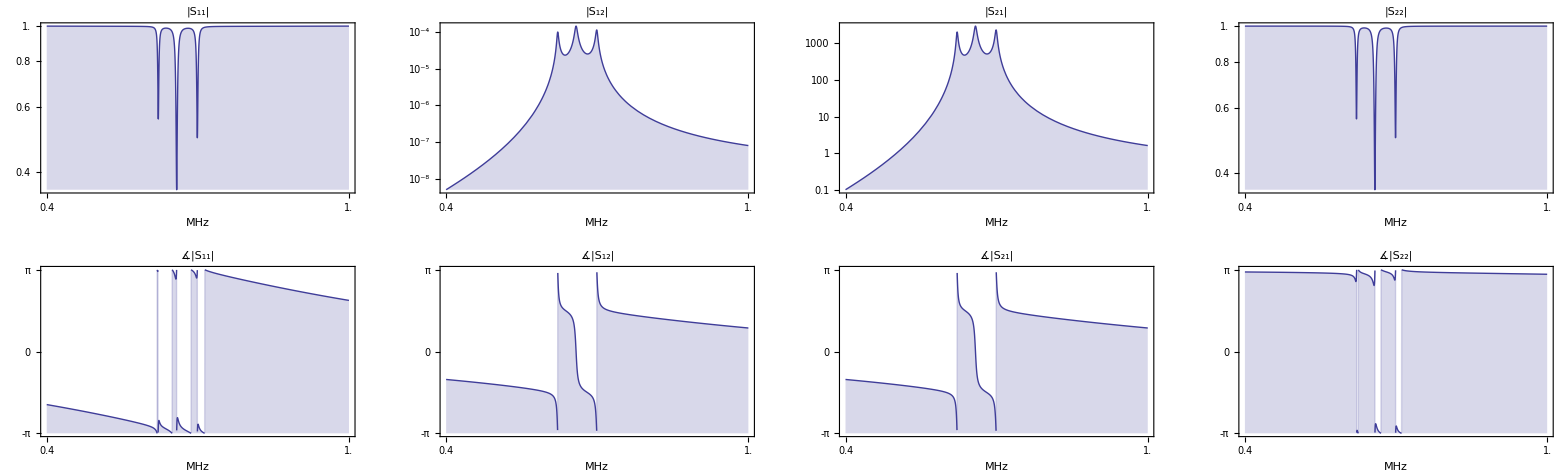

```mathematica
LogLinearPlotSparameters[baseCircuitExpressionSparam/.BasicCircuitParameters,{f,40 10^5,100 10^7}]
LogLinearPlotSparameters[doubleCircuitExpressionSparam/.BasicCircuitParameters,{f,58 10^6,62 10^6}]
LogLinearPlotSparameters[quadCircuitExpressionSparam/.BasicCircuitParameters,{f,40 10^6,100 10^6}]
```

```mathematica
SmithPlot[ToZ[quadCircuitExpression][[1,1]],{f, 40 10^6,100 10^6}]
```

$Aborted

### An inductively coupled resonator

```mathematica
inductivelyCoupledCircuit=CircuitCascade[TwoportSeries[OneportC[c2]],CircuitCascade[TwoportCoupledInductors[OneportL[l2],OneportL[l1],OneportL[m1]],TwoportSeries[OneportC[c1]]]]

CircuitGraphics[inductivelyCoupledCircuit,Frame->False]
```

```mathematica
inductivelyCoupledCircuitExpression=CircuitExpression[inductivelyCoupledCircuit,ω]
```

```mathematica
inductivelyCoupledCircuitSparam=ToS[inductivelyCoupledCircuitExpression,{50.,1}]/.{c2->10^-9,c1->10^-9,l2->10^-11,l1->10^-12,m1->10^0}//Simplify
```

```mathematica
LogLinearPlotSparameters[inductivelyCoupledCircuitSparam,{ω,10 10^3,1 10^5}]
```

### A waveguide

```mathematica
spar=ToS[TwoportWaveguideABCD[z0,β,l]]/.{z0->50ω,β->.1,l->2}
```

```mathematica
LogLinearPlotSparameters[spar,{ω,10^-9,10 10^6}]
```

### A metamaterial (NOT Working yet)

```mathematica
meta=CircuitCascade[CircuitCascade[CircuitCascade[CircuitCascade[CircuitCascade[TwoportSeries[OneportR[r1]],TwoportSeries[OneportL[l1]]],TwoportSeries[OneportC[c1]]],TwoportShunt[OneportR[r2]]],TwoportShunt[OneportL[l2]]],TwoportShunt[OneportC[c2]]]/.{r1->.0001,r2->.0001,l1->10^-12,l2->10^-12,c1->10^-6,c2->10^-6}
CircuitGraphics[meta]
mat=HighpassCircuitExpression=CircuitExpression[meta,ω]
γ=Log[Eigensystem[List@@mat][[1]]]
```

```mathematica
LogLogPlot[Arg[γ[[1]]],{ω,10^(-9),10^15},PlotRange->All,Frame->True]
LogLogPlot[Re[γ[[1]]],{ω,10^(-9),10^15},PlotRange->All,Frame->True]
LogLogPlot[Arg[γ[[2]]],{ω,10^(-9),10^15},PlotRange->All,Frame->True]
LogLogPlot[Re[γ[[2]]],{ω,10^(-9),10^15},PlotRange->All,Frame->True]
```

### A double resonant coil (NOT Working yet)

```mathematica
doubleResonantCircuit=CircuitCascade[CircuitCascade[TwoportShunt[OneportC[c1]] ,TwoportShunt[OneportL[l1]]],TwoportShunt[OneportSeries[OneportL[l2],OneportC[c2]]]]
CircuitGraphics[doubleResonantCircuit]
doubleResonantCircuitExpression=CircuitExpression[doubleResonantCircuit,ω]
MatrixForm[doubleResonantExpression]
doubleResonantCircuitExpressionSparam=ToS[doubleResonantCircuitExpression,{50.,1. 10^7}]//Chop
doubleResonantCircuitParameters={c1->10. 10^-10,l1->.2 10^-6,c2->1. 10^-10,l2->1 10^-6};
```

```mathematica
LogLinearPlotSparameters[doubleResonantCircuitExpressionSparam/.doubleResonantCircuitParameters,{ω,6 10^7, 1.5 10^8}]
```

### Reading (and using) touchstone files

#### List of all available touchstone file examples

```mathematica
SetDirectory["/Users/Jan G. Korvink/Desktop/DT/3 Temp Docs/CircuitTheory/TouchstoneExamples/"]
FileNames[{"*.s*p","*.ts"}]
```

#### Comprehensive touchstone file reading test

```mathematica
SetDirectory["/Users/Jan G. Korvink/Desktop/DT/3 Temp Docs/CircuitTheory/TouchstoneExamples/"]

(ReadTouchstone[StringJoin["/Users/Jan G. Korvink/Desktop/DT/3 Temp Docs/CircuitTheory/TouchstoneExamples/",ToString[#]]]&/@FileNames[{"*.s*p","*.ts"}])
```

#### Plotting a touchstone S-parameter file of a transistor (source: Oliver Gruschke)

```mathematica
PlotSparameters[ExtractTouchstoneNetwork[ReadTouchstone[StringJoin["/Users/Jan G. Korvink/Desktop/DT/3 Temp Docs/CircuitTheory/TouchstoneExamples/","f551432n.s2p"]]],{f, 1.1*^8, 1.7*^10}]
```

### Senn P 76

CircuitCascade[TwoportSeries[OneportC[1.2×10^-12]],CircuitCascade[TwoportSeries[OneportL[13/100000000]],CircuitCascade[TwoportShunt[OneportC[17/250000000000]],TwoportShunt[OneportL[2.4×10^-9]]]]]

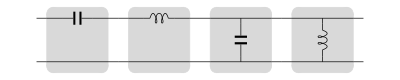

/Users/Jan G. Korvink/Desktop/DT/3 Temp Docs/CircuitTheory/senncircuit1pic.pdf

^A{{(55.1667+0. ⅈ)-1/ω(0.+8.33333×10^11 ⅈ) ((0.+0. ⅈ)-(0.+4.16667×10^8 ⅈ)/ω+(0.+6.8×10^-11 ⅈ) ω)-(8.84×10^-18+0. ⅈ) ω^2,-(0.+8.33333×10^11 ⅈ)/ω+(13 ⅈ ω)/100000000},{(0.+0. ⅈ)-(0.+4.16667×10^8 ⅈ)/ω+(0.+6.8×10^-11 ⅈ) ω,1}}

((55.1667+0. ⅈ)-((0.+8.33333×10^11 ⅈ) ((0.+0. ⅈ)-(0.+4.16667×10^8 ⅈ)/ω+(0.+6.8×10^-11 ⅈ) ω))/ω-(8.84×10^-18+0. ⅈ) ω^2 | -(0.+8.33333×10^11 ⅈ)/ω+(13 ⅈ ω)/100000000
(0.+0. ⅈ)-(0.+4.16667×10^8 ⅈ)/ω+(0.+6.8×10^-11 ⅈ) ω | 1)

^S{{(54.1667+1/50 (-(0.+8.33333×10^11 ⅈ)/ω+(13 ⅈ ω)/100000000)-(3.47222×10^20+0. ⅈ)/ω^2+(0.+2.08333×10^10 ⅈ)/ω)/(56.1667+1/50 (-(0.+8.33333×10^11 ⅈ)/ω+(13 ⅈ ω)/100000000)-(3.47222×10^20+0. ⅈ)/ω^2-(0.+2.08333×10^10 ⅈ)/ω),(2. (55.1667-(3.47222×10^20+0. ⅈ)/ω^2+((0.+4.16667×10^8 ⅈ) (-(0.+8.33333×10^11 ⅈ)/ω+(13 ⅈ ω)/100000000))/ω))/(56.1667+1/50 (-(0.+8.33333×10^11 ⅈ)/ω+(13 ⅈ ω)/100000000)-(3.47222×10^20+0. ⅈ)/ω^2-(0.+2.08333×10^10 ⅈ)/ω)},{2./(56.1667+1/50 (-(0.+8.33333×10^11 ⅈ)/ω+(13 ⅈ ω)/100000000)-(3.47222×10^20+0. ⅈ)/ω^2-(0.+2.08333×10^10 ⅈ)/ω),(-54.1667+1/50 (-(0.+8.33333×10^11 ⅈ)/ω+(13 ⅈ ω)/100000000)+(3.47222×10^20+0. ⅈ)/ω^2+(0.+2.08333×10^10 ⅈ)/ω)/(56.1667+1/50 (-(0.+8.33333×10^11 ⅈ)/ω+(13 ⅈ ω)/100000000)-(3.47222×10^20+0. ⅈ)/ω^2-(0.+2.08333×10^10 ⅈ)/ω)}}

```mathematica
sennCircuit1=CircuitCascade[TwoportSeries[OneportC[1.2 10^-12]],CircuitCascade[TwoportSeries[OneportL[130 10^-9]],CircuitCascade[TwoportShunt[OneportC[68 10^-12]],TwoportShunt[OneportL[2.4 10^-9]]]]]
senncircuit1pic=CircuitGraphics[sennCircuit1]
Export["/Users/Jan G. Korvink/Desktop/DT/3 Temp Docs/CircuitTheory/senncircuit1pic.pdf",senncircuit1pic]
sennCircuit1Expression=CircuitExpression[sennCircuit1,ω]
MatrixForm[sennCircuit1Expression]
sennCircuit1ExpressionSparam=ToS[sennCircuit1Expression,{50.,50}]//Chop
```

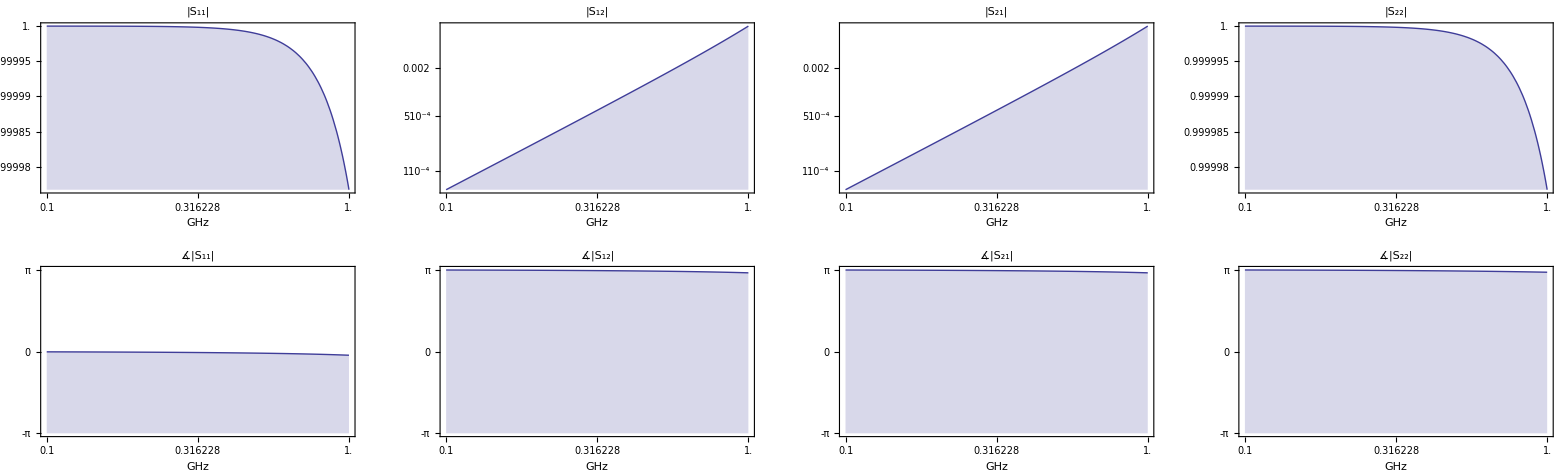

```mathematica
LogLinearPlotSparameters[sennCircuit1ExpressionSparam,{ω,1 10^8, 10 10^8}]
```

```mathematica
ToH[sennCircuit1Expression]
```

^H{{-(0.+8.33333×10^11 ⅈ)/ω+(0.+1.3×10^-7 ⅈ) ω,1.+0. ⅈ},{1,(0.+0. ⅈ)+(0.+4.16667×10^8 ⅈ)/ω-(0.+6.8×10^-11 ⅈ) ω}}

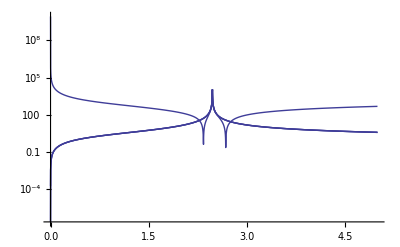

```mathematica
LogPlot[Abs[List@@ToZ[sennCircuit1Expression]],{ω,1 10^0, 5 10^9},PlotRange->All]
```

```mathematica
sennCircuit1
```

CircuitCascade[TwoportSeries[OneportC[1.2×10^-12]],CircuitCascade[TwoportSeries[OneportL[13/100000000]],CircuitCascade[TwoportShunt[OneportC[17/250000000000]],TwoportShunt[OneportL[2.4×10^-9]]]]]

```mathematica
sennCircuit1/.OneportConversionRules[ω]/.TwoportConversionRules
```

CircuitCascade[^A{{1,-(0.+8.33333×10^11 ⅈ)/ω},{0,1}},CircuitCascade[^A{{1,(13 ⅈ ω)/100000000},{0,1}},CircuitCascade[^A{{1,0},{(17 ⅈ ω)/250000000000,1}},^A{{1,0},{-(0.+4.16667×10^8 ⅈ)/ω,1}}]]]

### Senn P 84

CircuitCascade[TwoportShunt[OneportL[1.5×10^-9]],CircuitCascade[TwoportShunt[OneportC[1/10000000000]],CircuitCascade[TwoportSeries[OneportC[6.8×10^-12]],CircuitCascade[TwoportShunt[OneportL[33/1000000000]],TwoportSeries[OneportL[17/250000000]]]]]]

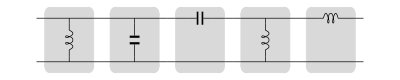

/Users/Jan G. Korvink/Desktop/DT/3 Temp Docs/CircuitTheory/senncircuit5pic.pdf

^A{{1-(4.45633×10^18+0. ⅈ)/ω^2,-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω},{-(0.+4.75936×10^8 ⅈ)/ω-((0.+6.66667×10^8 ⅈ) (1-(4.45633×10^18+0. ⅈ)/ω^2))/ω+(0.+1.×10^-10 ⅈ) ω,(48.0695+0. ⅈ)-((0.+6.66667×10^8 ⅈ) (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω))/ω-(6.8×10^-18+0. ⅈ) ω^2}}

(1-(4.45633×10^18+0. ⅈ)/ω^2 | -(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω
-(0.+4.75936×10^8 ⅈ)/ω-((0.+6.66667×10^8 ⅈ) (1-(4.45633×10^18+0. ⅈ)/ω^2))/ω+(0.+1.×10^-10 ⅈ) ω | (48.0695+0. ⅈ)-((0.+6.66667×10^8 ⅈ) (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω))/ω-(6.8×10^-18+0. ⅈ) ω^2)

^S{{(-47.0695-50 (-(0.+4.75936×10^8 ⅈ)/ω-((0.+6.66667×10^8 ⅈ) (1-(4.45633×10^18)/ω^2))/ω)+1/50 (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω)-(4.45633×10^18)/ω^2+1/ω(0.+6.66667×10^8 ⅈ) (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω))/(49.0695+50 (-(0.+4.75936×10^8 ⅈ)/ω-((0.+6.66667×10^8 ⅈ) (1-(4.45633×10^18)/ω^2))/ω)+1/50 (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω)-(4.45633×10^18)/ω^2-1/ω(0.+6.66667×10^8 ⅈ) (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω)),(0.00447214 ((1-(4.45633×10^18)/ω^2) (48.0695-1/ω(0.+6.66667×10^8 ⅈ) (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω))-(-(0.+4.75936×10^8 ⅈ)/ω-((0.+6.66667×10^8 ⅈ) (1-(4.45633×10^18)/ω^2))/ω) (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω)))/(49.0695+50 (-(0.+4.75936×10^8 ⅈ)/ω-((0.+6.66667×10^8 ⅈ) (1-(4.45633×10^18)/ω^2))/ω)+1/50 (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω)-(4.45633×10^18)/ω^2-1/ω(0.+6.66667×10^8 ⅈ) (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω))},{894.427/(49.0695+50 (-(0.+4.75936×10^8 ⅈ)/ω-((0.+6.66667×10^8 ⅈ) (1-(4.45633×10^18)/ω^2))/ω)+1/50 (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω)-(4.45633×10^18)/ω^2-1/ω(0.+6.66667×10^8 ⅈ) (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω)),(47.0695-50 (-(0.+4.75936×10^8 ⅈ)/ω-((0.+6.66667×10^8 ⅈ) (1-(4.45633×10^18)/ω^2))/ω)+1/50 (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω)+(4.45633×10^18)/ω^2-1/ω(0.+6.66667×10^8 ⅈ) (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω))/(49.0695+50 (-(0.+4.75936×10^8 ⅈ)/ω-((0.+6.66667×10^8 ⅈ) (1-(4.45633×10^18)/ω^2))/ω)+1/50 (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω)-(4.45633×10^18)/ω^2-1/ω(0.+6.66667×10^8 ⅈ) (-(0.+4.50089×10^11 ⅈ)/ω+(0.+6.8×10^-8 ⅈ) ω))}}

```mathematica
sennCircuit5=CircuitCascade[TwoportShunt[OneportL[1.5 10^-9]],CircuitCascade[TwoportShunt[OneportC[100 10^-12]],CircuitCascade[TwoportSeries[OneportC[6.8 10^-12]],CircuitCascade[TwoportShunt[OneportL[33 10^-9]],TwoportSeries[OneportL[68 10^-9]]]]]]
senncircuit5pic=CircuitGraphics[sennCircuit5]
Export["/Users/Jan G. Korvink/Desktop/DT/3 Temp Docs/CircuitTheory/senncircuit5pic.pdf",senncircuit5pic]
sennCircuit5Expression=CircuitExpression[sennCircuit5,ω]
MatrixForm[sennCircuit5Expression]
sennCircuit5ExpressionSparam=ToS[sennCircuit5Expression,{50.,1. 10^7}]//Chop
```

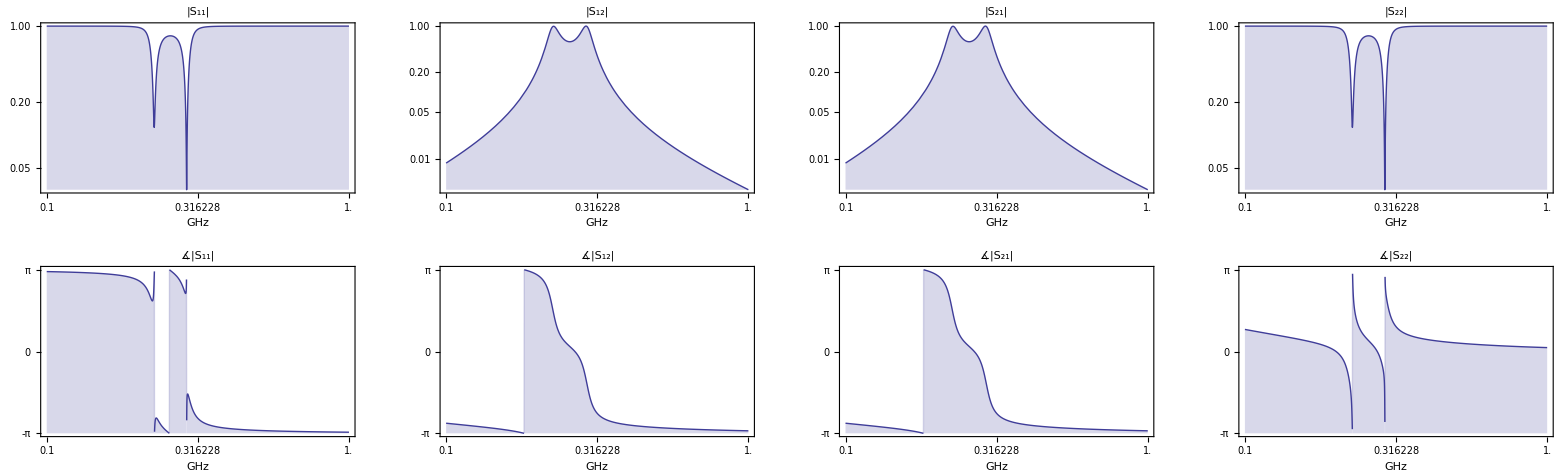

```mathematica
LogLinearPlotSparameters[ToS[sennCircuit5Expression],{ω,1 10^9, 10^10}]
```

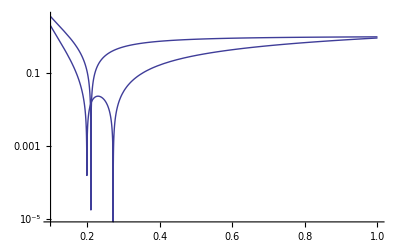

```mathematica
LogPlot[Abs[sennCircuit5Expression.{1,0}],{ω,1 10^9, 10^10},PlotRange->All]
```

```mathematica
ToH[sennCircuit5Expression]
```

^H{{(ω ((0.-4.50089×10^11 ⅈ)+(0.+6.8×10^-8 ⅈ) ω^2))/((-3.00059×10^20+0. ⅈ)+(93.4029+0. ⅈ) ω^2-(6.8×10^-18+0. ⅈ) ω^4),((131072.+0. ⅈ)+(1.+0. ⅈ) ω^2-(7.70372×10^-34+0. ⅈ) ω^4)/((-3.00059×10^20+0. ⅈ)+(93.4029+0. ⅈ) ω^2-(6.8×10^-18+0. ⅈ) ω^4)},{ω^2/((-3.00059×10^20+0. ⅈ)+(93.4029+0. ⅈ) ω^2-(6.8×10^-18+0. ⅈ) ω^4),((0.+2.97089×10^27 ⅈ)-(0.+1.1426×10^9 ⅈ) ω^2+(0.+1.×10^-10 ⅈ) ω^4)/((3.00059×10^20+0. ⅈ) ω-(93.4029+0. ⅈ) ω^3+(6.8×10^-18+0. ⅈ) ω^5)}}

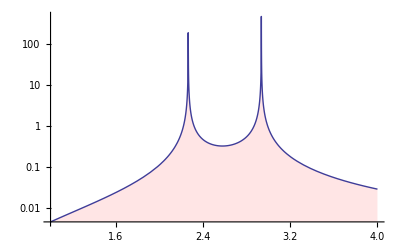

```mathematica
LogPlot[Tooltip[Abs[ToH[sennCircuit5Expression][[1,2]]]],{ω,1 10^9, 4 10^9},PlotRange->All,FillingStyle->{Opacity[.1,Red]},Filling->Bottom]
```

### A cable trap

TwoportSeries[OneportShortedStub[50,π/40,0.00001]]

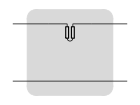

^A{{1,(0.+0.00024674 ⅈ) f},{0,1}}

^S{{((0.+4.9348×10^-6 ⅈ) f)/(2+(0.+4.9348×10^-6 ⅈ) f),(4.47214×10^-8+0. ⅈ)/(2+(0.+4.9348×10^-6 ⅈ) f)},{(8.94427×10^7)/(2+(0.+4.9348×10^-6 ⅈ) f),((0.+4.9348×10^-6 ⅈ) f)/(2+(0.+4.9348×10^-6 ⅈ) f)}}

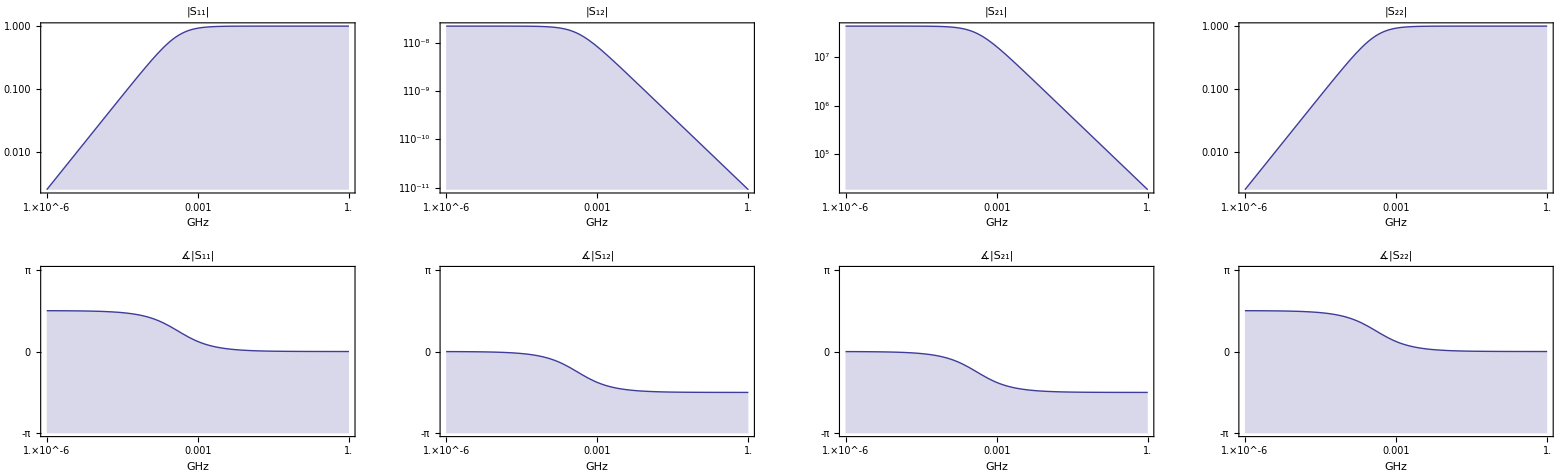

```mathematica
circuit=TwoportSeries[OneportShortedStub[50,π/40,.00001]]
CircuitGraphics[circuit]
expression=CircuitExpression[circuit,2π f]
sparam=ToS[expression,{50.,1. 10^17}]
LogLinearPlotSparameters[sparam,{f, 10^3, 10^9}]
```

TwoportShunt[OneportShortedStub[50,π/40,0.00001]]

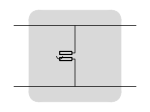

^A{{1,0},{-(0.+4052.85 ⅈ)/f,1}}

^S{{(0.+202642. ⅈ)/((2-(0.+202642. ⅈ)/f) f),(4.47214×10^-8+0. ⅈ)/(2-(0.+202642. ⅈ)/f)},{(8.94427×10^7)/(2-(0.+202642. ⅈ)/f),(0.+202642. ⅈ)/((2-(0.+202642. ⅈ)/f) f)}}

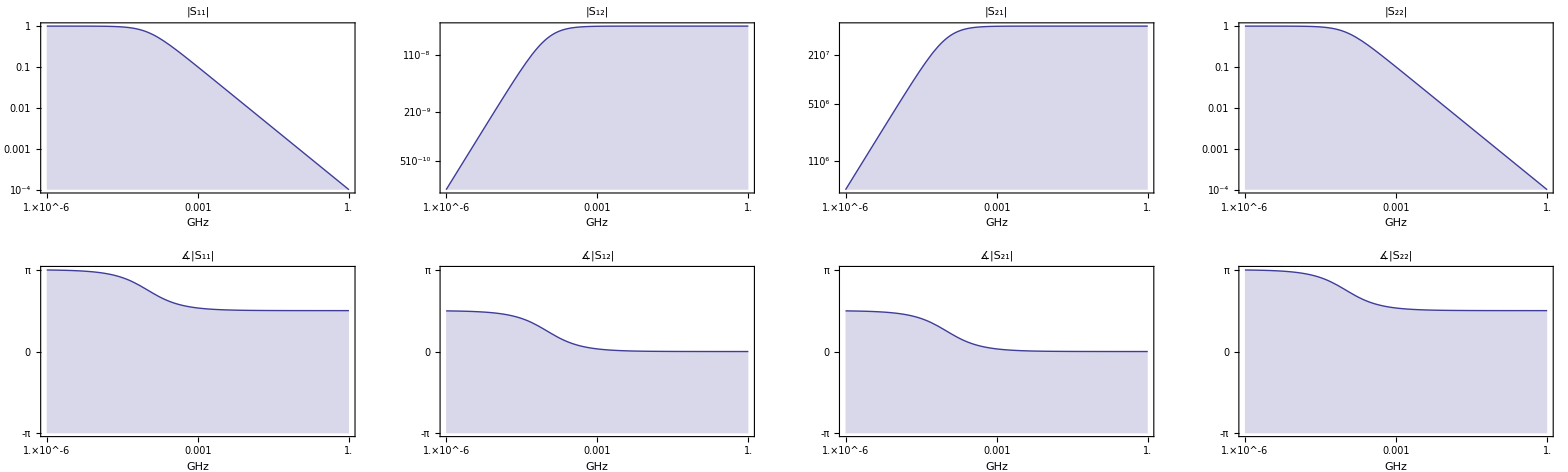

```mathematica
circuit=TwoportShunt[OneportShortedStub[50,π/40,.00001]]
CircuitGraphics[circuit]
expression=CircuitExpression[circuit,2π f]
sparam=ToS[expression,{50.,1. 10^17}]
LogLinearPlotSparameters[sparam,{f, 10^3, 10^9}]
```

### Jan’s current tests

```mathematica
TwoportLossyWaveguideABCD[1,2,3]
TwoportWaveguideABCD[1,2,3]
TwoportBoxsectionABCD[z1,z2]
TwoportCsectionABCD[z1,z2]
TwoportHsectionABCD[z1,z2]
TwoportUnbalancedLadderABCD[z1,z2,3]
```

```mathematica
CircuitGraphics[TwoportShunt[OneportOpenStub[1,1,1]]]
CircuitGraphics[TwoportShunt[OneportShortedStub[1,1,1]]]
```

```mathematica
c=CircuitCascade[CircuitCascade[TwoportSeries[OneportL[1]],TwoportInvert[]],CircuitCascade[TwoportSeries[OneportL[1]],TwoportInvert[]]];
c=TwoportSeries[OneportL[1]];
CircuitGraphics[c]
CircuitExpression[c]
```

```mathematica
TwoportSeriesABCD[ⅈ ω l1]
```

```mathematica
ToZ[ABCD[{a,b},{c,d}]]
```

```mathematica
(ToA[Z@@(List[{0,1},{1,0}].(List@@ToZ[ABCD[{a,b},{c,d}]]).List[{0,1},{1,0}])])
```

```mathematica
/.{a->1,b->ⅈ l1 ω,c->0,d->1}
```

```mathematica
TwoportInvertABCD[]
TwoportSeriesABCD[ⅈ ω l1].TwoportSeriesABCD[ⅈ ω l2]
TwoportSeriesABCD[ⅈ ω l1].TwoportInvertABCD[].TwoportSeriesABCD[ⅈ ω l2].TwoportInvertABCD[]
```

```mathematica
?Circuit*
```

```mathematica
?OneportL
```

```mathematica
Flatten[{{Subscript[z, 11]->zz,Subscript[z, 12]->-zz,Subscript[z, 13]->0,Subscript[z, 14]->0},{Subscript[z, 21]->-zz,Subscript[z, 22]->zz,Subscript[z, 23]->0,Subscript[z, 24]->0},{Subscript[z, 31]->0,Subscript[z, 32]->0,Subscript[z, 33]->∞,Subscript[z, 34]->-∞},{Subscript[z, 41]->0,Subscript[z, 42]->0,Subscript[z, 43]->-∞,Subscript[z, 44]->∞}}]
```

```mathematica
{Subscript[z, 11]->zz,Subscript[z, 12]->-zz,Subscript[z, 13]->0,Subscript[z, 14]->0,Subscript[z, 21]->-zz,Subscript[z, 22]->zz,Subscript[z, 23]->0,Subscript[z, 24]->0,Subscript[z, 31]->0,Subscript[z, 32]->0,Subscript[z, 33]->0,Subscript[z, 34]->0,Subscript[z, 41]->0,Subscript[z, 42]->0,Subscript[z, 43]->-∞,Subscript[z, 44]->∞}
```

```mathematica
Bb={{1,0,-1,0},{0,1,0,-1}};
Cc={{1,0,1,0},{0,1,0,1}};
Z={{Subscript[z, 11],Subscript[z, 12],Subscript[z, 13],Subscript[z, 14]},{Subscript[z, 21],Subscript[z, 22],Subscript[z, 23],Subscript[z, 24]},{Subscript[z, 31],Subscript[z, 32],Subscript[z, 33],Subscript[z, 34]},{Subscript[z, 41],Subscript[z, 42],Subscript[z, 43],Subscript[z, 44]}}
ToA[(Z@@(Bb.Z.PseudoInverse[Cc]//Simplify)/.Flatten[{{Subscript[z, 11]->s,Subscript[z, 12]->-s,Subscript[z, 13]->b,Subscript[z, 14]->b},{Subscript[z, 21]->-s,Subscript[z, 22]->s,Subscript[z, 23]->b,Subscript[z, 24]->b},{Subscript[z, 31]->b,Subscript[z, 32]->b,Subscript[z, 33]->zz,Subscript[z, 34]->-zz},{Subscript[z, 41]->b,Subscript[z, 42]->b,Subscript[z, 43]->-zz,Subscript[z, 44]->zz}}])]/.{s->0}
ToA[(Z@@(Bb.Z.PseudoInverse[Cc]//Simplify)/.Flatten[{{Subscript[z, 11]->zz,Subscript[z, 12]->-zz,Subscript[z, 13]->b,Subscript[z, 14]->b},{Subscript[z, 21]->-zz,Subscript[z, 22]->zz,Subscript[z, 23]->b,Subscript[z, 24]->b},{Subscript[z, 31]->b,Subscript[z, 32]->b,Subscript[z, 33]->s,Subscript[z, 34]->-s},{Subscript[z, 41]->b,Subscript[z, 42]->b,Subscript[z, 43]->-s,Subscript[z, 44]->s}}])]/.{s->0}
```

```mathematica
TwoportSeriesABCD[zz]
```

```mathematica
CircuitGraphics[TwoportSeriesDown[OneportShortedStub[1,1,1]]]
```

```mathematica
Graphics[CircuitGraphics[TwoportSeriesDown[OneportL[1]]]]
```

```mathematica
CircuitExpression[CircuitCascade[TwoportSeries[OneportL[1]],TwoportSeriesDown[OneportL[1]]]]
```

```mathematica
TwoportShuntABCD[OneportL[n]].TwoportSeriesABCD[OneportL[l]].TwoportSeriesDownABCD[OneportL[m]].TwoportShuntABCD[OneportL[n]]
```

```mathematica
OneportL[l]
```

```mathematica
MatrixForm[{{1,0},{0,1}}]
```

(1 | 0
0 | 1)

```mathematica
LongForm[({{1, 0}, {0, 1}})]
```

LongForm[{{1,0},{0,1}}]

```mathematica
?*Form
```

RowBox[{"TableForm", "[", StyleBox["list", "TI"], "]"}] prints with the elements of StyleBox["list", "TI"] arranged in an array of rectangular cells.

```mathematica
?\Left
```

Information::nomatch: No symbol matching "\\Left" found.

### The probehead course example

```mathematica
MRCircuit=CircuitCascade[TwoportShunt[Zc] ,TwoportSeries[Z1],TwoportShunt[Z2],TwoportSeries[Z1]]
MRCircuitExpression=CircuitExpression[MRCircuit,ω];
```

CircuitCascade[TwoportShunt[Zc],TwoportSeries[Z1],TwoportShunt[Z2],TwoportSeries[Z1]]

```mathematica
(List@@MRCircuitExpression)//TeXForm
((MRCircuitExpressionSparam=ToS[MRCircuitExpression,{50.,50}])[[1,1]])//TeXForm
```

\frac{-50
   \left(\frac{\frac{\text{Z1}}{\text{Zc}}+1}{\text{Z2}}+
   \frac{1}{\text{Zc}}\right)-\left(\frac{\text{Z1}}{\tex
   t{Z2}}+1\right)
   \left(\frac{\text{Z1}}{\text{Zc}}+1\right)+\frac{\text
   {Z1}}{\text{Z2}}+\frac{1}{50} \left(\text{Z1}
   \left(\frac{\text{Z1}}{\text{Z2}}+1\right)+\text{Z1}\r
   ight)-\frac{\text{Z1}}{\text{Zc}}+1}{50
   \left(\frac{\frac{\text{Z1}}{\text{Zc}}+1}{\text{Z2}}+
   \frac{1}{\text{Zc}}\right)+\left(\frac{\text{Z1}}{\tex
   t{Z2}}+1\right)
   \left(\frac{\text{Z1}}{\text{Zc}}+1\right)+\frac{\text
   {Z1}}{\text{Z2}}+\frac{1}{50} \left(\text{Z1}
   \left(\frac{\text{Z1}}{\text{Z2}}+1\right)+\text{Z1}\r
   ight)+\frac{\text{Z1}}{\text{Zc}}+1}

```mathematica
(List@@MRCircuitExpression)//TeXForm
((MRCircuitExpressionSparam=ToS[MRCircuitExpression,{50.,50}])[[1,2]])//TeXForm
```

\frac{2. \left(\left(\frac{\text{Z1}}{\text{Z2}}+1\right)
   \left(\left(\frac{\text{Z1}}{\text{Z2}}+1\right)
   \left(\frac{\text{Z1}}{\text{Zc}}+1\right)+\frac{\text
   {Z1}}{\text{Zc}}\right)-\left(\text{Z1}
   \left(\frac{\text{Z1}}{\text{Z2}}+1\right)+\text{Z1}\r
   ight)
   \left(\frac{\frac{\text{Z1}}{\text{Zc}}+1}{\text{Z2}}+
   \frac{1}{\text{Zc}}\right)\right)}{50
   \left(\frac{\frac{\text{Z1}}{\text{Zc}}+1}{\text{Z2}}+
   \frac{1}{\text{Zc}}\right)+\left(\frac{\text{Z1}}{\tex
   t{Z2}}+1\right)
   \left(\frac{\text{Z1}}{\text{Zc}}+1\right)+\frac{\text
   {Z1}}{\text{Z2}}+\frac{1}{50} \left(\text{Z1}
   \left(\frac{\text{Z1}}{\text{Z2}}+1\right)+\text{Z1}\r
   ight)+\frac{\text{Z1}}{\text{Zc}}+1}

CircuitCascade[TwoportShunt[OneportC[c1]],TwoportSeries[OneportL[l1-m]],TwoportShunt[OneportL[m]],TwoportSeries[OneportL[l1-m]]]

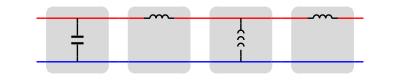

^A{{1+(l1-m)/m,ⅈ (l1-m) ω+ⅈ (1+(l1-m)/m) (l1-m) ω},{ⅈ c1 ω-(ⅈ (1-c1 (l1-m) ω^2))/(m ω),-c1 (l1-m) ω^2+(1+(l1-m)/m) (1-c1 (l1-m) ω^2)}}

(1+(l1-m)/m | ⅈ (l1-m) ω+ⅈ (1+(l1-m)/m) (l1-m) ω
ⅈ c1 ω-(ⅈ (1-c1 (l1-m) ω^2))/(m ω) | -c1 (l1-m) ω^2+(1+(l1-m)/m) (1-c1 (l1-m) ω^2))

```mathematica
MRCircuit=CircuitCascade[TwoportShunt[OneportC[c1]] ,TwoportSeries[OneportL[l1-m]],TwoportShunt[OneportL[m]],TwoportSeries[OneportL[l1-m]]]
mrcircuitpic=CircuitGraphics[MRCircuit]
(*Export["/Users/Jan G. Korvink/Desktop/DT/3 Temp Docs/CircuitTheory/mrcircuitpic.pdf",mrcircuitpic]*)
MRCircuitExpression=CircuitExpression[MRCircuit,ω]
MatrixForm[MRCircuitExpression]
MRCircuitExpressionSparam=ToS[MRCircuitExpression,{50.,50}]//Chop;
MRCircuitParameters={c1->10. 10^-10,l1->.15 10^-7,m->0.01*.15 10^-7};
```

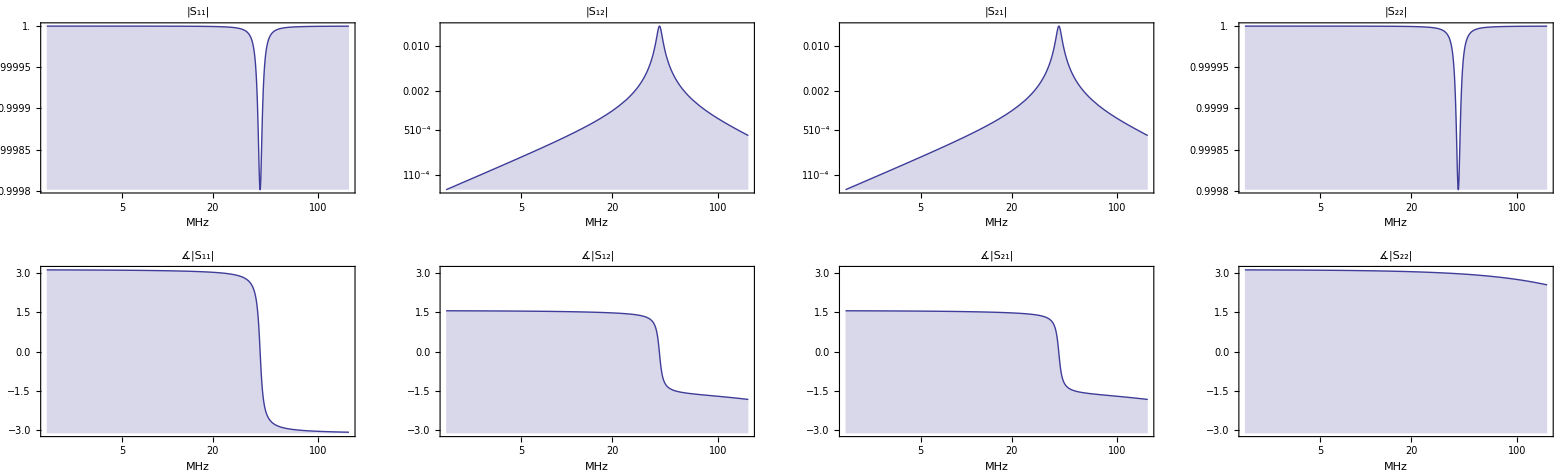

```mathematica
sparamplot=LogLinearPlotSparameters[MRCircuitExpressionSparam/.MRCircuitParameters,{ω,1 10^7, 10^9}]
```

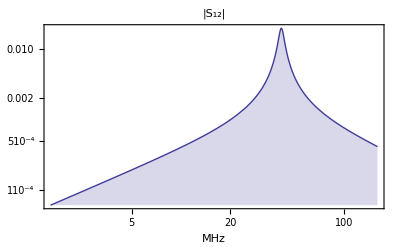

/Users/korvink1/SynchWithVoxalyticCom/KorvinkFiles/3 Temp Docs/S12.pdf

```mathematica
sparamplot[[1,2,1,2,1]]
Export["/Users/korvink1/SynchWithVoxalyticCom/KorvinkFiles/3 Temp Docs/S12.pdf",sparamplot[[1,2,1,2,1]]]
```

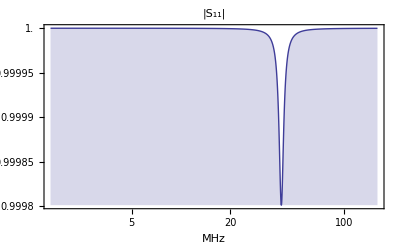

/Users/korvink1/SynchWithVoxalyticCom/KorvinkFiles/3 Temp Docs/S11.pdf

```mathematica
sparamplot[[1,2,1,1,1]]
Export["/Users/korvink1/SynchWithVoxalyticCom/KorvinkFiles/3 Temp Docs/S11.pdf",sparamplot[[1,2,1,1,1]]]
```

```mathematica
(MRCircuitExpressionSparam/.MRCircuitParameters)[[1,2]]
```

(2. (100. (-1.485×10^-17 ω^2+100. (1-1.485×10^-17 ω^2))-(0.+1.49985×10^-6 ⅈ) ω ((0.+1.×10^-9 ⅈ) ω-((0.+6.66667×10^9 ⅈ) (1-1.485×10^-17 ω^2))/ω)))/(100.+(0.+2.9997×10^-8 ⅈ) ω-1.485×10^-17 ω^2+100. (1-1.485×10^-17 ω^2)+50 ((0.+1.×10^-9 ⅈ) ω-((0.+6.66667×10^9 ⅈ) (1-1.485×10^-17 ω^2))/ω))

```mathematica
(MRCircuitExpressionSparam/.MRCircuitParameters)[[1,2]]
```

(2. (100. (-1.485×10^-17 ω^2+100. (1-1.485×10^-17 ω^2))-(0.+1.49985×10^-6 ⅈ) ω ((0.+1.×10^-9 ⅈ) ω-((0.+6.66667×10^9 ⅈ) (1-1.485×10^-17 ω^2))/ω)))/(100.+(0.+2.9997×10^-8 ⅈ) ω-1.485×10^-17 ω^2+100. (1-1.485×10^-17 ω^2)+50 ((0.+1.×10^-9 ⅈ) ω-((0.+6.66667×10^9 ⅈ) (1-1.485×10^-17 ω^2))/ω))

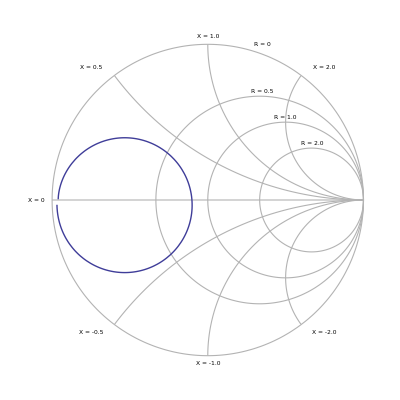

```mathematica
SmithPlot[1+2000(MRCircuitExpressionSparam/.MRCircuitParameters)[[1,2]],{ω,1 10^7, 10^9}]
```

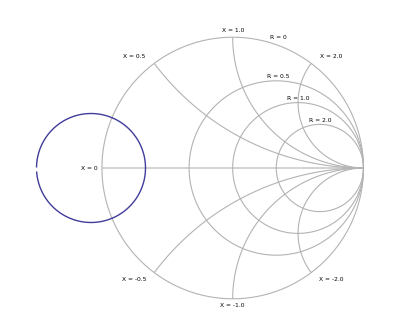

```mathematica
SmithPlot[10(MRCircuitExpressionSparam/.MRCircuitParameters)[[1,1]],{ω,1 10^7, 10^9}]
```

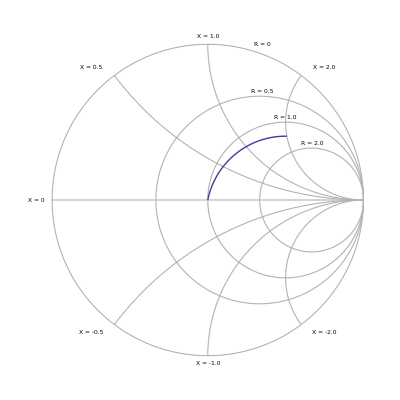

```mathematica
SmithPlot[50+(.2+ⅈ) ω 10^(-9),{ω,1 10^0, 10^11}]
```

### A double resonant probe

```mathematica
doubleResonantCircuit=CircuitCascade[TwoportShunt[OneportC[c2]],TwoportShunt[OneportC[c2]]]
```

CircuitCascade[TwoportShunt[OneportC[c2]],TwoportShunt[OneportC[c2]]]

```mathematica
CircuitGraphics[doubleResonantCircuit]
```

CircuitGraphics[CircuitCascade[TwoportShunt[OneportC[c2]],TwoportShunt[OneportC[c2]]]]

```mathematica
bridgeCircuitExpression=CircuitExpression[doubleResonantCircuit,ω]/.{r1->10000,r2->20000,r3->10000,r4->40000,l1->10^(-9),c1->10^(-12)}
```

^A{{-15/2-110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000),-110000},{-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000),-6}}

```mathematica
bridgeCircuitExpressionSparam=ToS[bridgeCircuitExpression,{50.,1. 10^18}]//Chop
```

^S{{(-4403/2-50 (-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))-110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))/(-4427/2+50 (-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))-110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000)),(1.41421×10^-8 (-6 (-15/2-110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))+110000 (-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))))/(-4427/2+50 (-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))-110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))},{2.82843×10^8/(-4427/2+50 (-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))-110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000)),(-4397/2-50 (-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))+110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))/(-4427/2+50 (-1/2500-6 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))-110000 (-(1000000000 ⅈ)/ω+(ⅈ ω)/1000000000000))}}

```mathematica
omin=10^10;omax=1 10^11;
LogLinearPlotSparameters[bridgeCircuitExpressionSparam,{ω,omin,omax}]
```

-Graphics-